```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
ρ=N[1-1/10^9];
SIGMA=Table[ρ,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/ρ];
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[Simplify[GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[Simplify[HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
```

10011233.729.255020.5826260.38388812.41251246.141.70474×10^119.84973×10^-72.55477×10^-6True{1,4}{1,4}

20021.16436×10^113.377610.3100010.48220518.55922910.481.16436×10^115.55992×10^-72.11138×10^-6False{1,3}{1,4}

30034654.2912.78680.6985440.52213714.25064668.547.22977×10^103.45227×10^-73.40039×10^-6True{1}{4}

40044.93803×10^103.529430.2024320.17926110.68434430.34.93803×10^101.331×10^-76.02401×10^-6False{3,4}{1}

500567057.914.43650.8943790.10986218.950567076.91.30034×10^108.26446×10^-85.47637×10^-6True{1,4}{1,4}

60069.76963×10^936.27810.7085230.50485320.2848280139.9.76963×10^93.50494×10^-86.62641×10^-6False{2,4}{1,4}

7007496260.16.98740.4004650.45374712.0283496272.4.48912×10^103.18631×10^-84.52593×10^-6True{1,3,4}{1,4}

80084.48912×10^1011.00720.6525240.52114111.96724.03968×10^64.48912×10^101.63508×10^-83.09127×10^-6False{1,4}{1,4}

90099.52531×10^616.30690.7102010.50194710.48189.52532×10^67.34007×10^99.2296×10^-97.28905×10^-6True{1}{4}

100108.07408×10^94.172940.6715660.30346212.28381.51101×10^88.07408×10^92.20949×10^-95.47637×10^-6False{1,2,3}{1,4}

110111.51101×10^88.921380.2716030.1734717.95591.51101×10^88.07408×10^92.20949×10^-95.47637×10^-6True{1,2,3}{1,4}

120128.07408×10^93.750380.4012280.52400717.65061.51101×10^88.07408×10^92.20949×10^-95.47637×10^-6False{1,2,3}{1,4}

130131.51101×10^826.86320.567520.43758510.82031.51101×10^88.07408×10^92.20949×10^-95.47637×10^-6True{1,2,3}{1,4}

140148.07408×10^99.403130.6859150.27207413.55351.51101×10^88.07408×10^92.20949×10^-95.47637×10^-6False{1,2,3}{1,4}

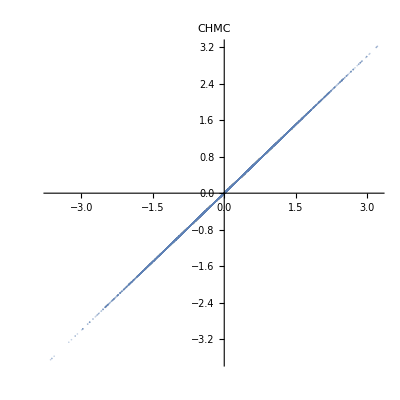

{1.07484,1.0007,1.00883,1.03481,0.996761,1.02483,0.95724,0.970028,1.01917,1.01059}

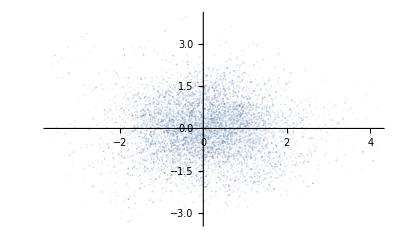

```mathematica
CHAINS=3;
STEPS=3;
QS=hmc[U,dU,ddU,10,5000,10000,True,True,{}];
ListPlot[QS[[;;,1;;2]],PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```

10013376.7913.71370.3215610.21630412.57433389.361.54559×10^104.59497×10^-71.×10^-7True{1,2,4}{1,4}

200236542.612.57210.8838870.20111413.257536555.91.54559×10^101.21×10^-71.×10^-7True{1,3}{1,4}

3003771518.9.924590.176710.17825813.5741771532.1.54559×10^103.18631×10^-81.×10^-7True{1}{4}

40041.36678×10^69.687960.5410530.28257717.7371.3668×10^61.54559×10^101.97845×10^-81.×10^-7True{1}{4}

50053.49181×10^715.35960.4181650.25650110.76963.49181×10^71.54559×10^103.23492×10^-91.×10^-7True{1}{4}

60063.49181×10^717.56180.8126820.32444416.36723.49181×10^71.54559×10^103.23492×10^-91.×10^-7True{1}{4}

70073.49181×10^712.20920.3959010.18593411.45013.49181×10^71.54559×10^103.23492×10^-91.×10^-7True{1}{4}

80083.49181×10^712.07670.7714280.36182922.58063.49181×10^71.54559×10^103.23492×10^-91.×10^-7True{1}{4}

90093.49181×10^718.53170.4466840.40367710.59153.49181×10^71.54559×10^103.23492×10^-91.×10^-7True{1}{4}

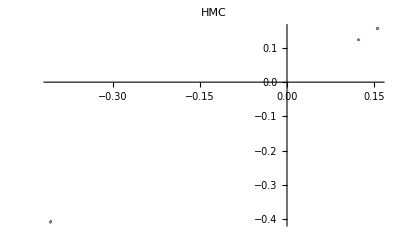

{0.93461,0.923964,0.924572,0.937242,0.942862,0.977958,0.936393,0.990475,0.889946,0.95898}

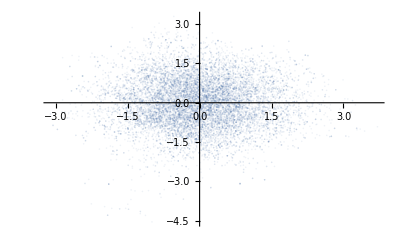

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,True,False,{}];
ListPlot[QS[[;;,1;;2]],PlotLabel->HMC,PlotStyle->Opacity[.1]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```

1001145.8718.710680.4261330.5130672.615681.2848×10^10148.4871.×10^-70.0468595False{2,4}{1,4}

2002211.72619.55890.6885320.5394780.977171.2848×10^10212.7031.×10^-70.0425996False{1,3}{1,4}

3003788.58733.4580.4195840.3671731.232711.2848×10^10789.821.×10^-70.0180664False{1}{4}

4004441.95111.59720.354840.515590.1378381.2848×10^10442.0891.×10^-70.0425996False{1,4}{1,4}

5005323.41513.38360.8650770.1374435.589981.2848×10^10329.0051.×10^-70.0387269False{1}{4}

6006328.55312.42190.4514370.3011790.4512871.2848×10^10329.0051.×10^-70.0387269False{1}{4}

7007324.349.368060.3698960.5478664.665011.2848×10^10329.0051.×10^-70.0387269False{1}{4}

8008327.19724.50670.1540760.1908651.807651.2848×10^10329.0051.×10^-70.0387269False{1}{4}

9009328.72329.90430.4617860.4678250.281281.2848×10^10329.0051.×10^-70.0387269False{1}{4}

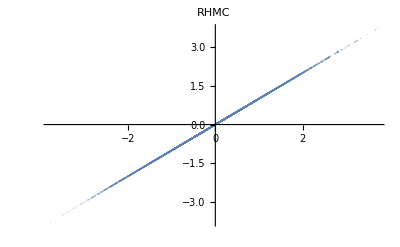

{0.314869,0.314867,0.314871,0.314873,0.31486,0.314867,0.31485,0.314868,0.314867,0.314859}

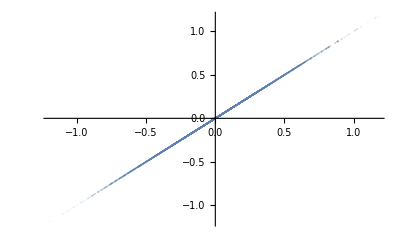

```mathematica
QS=hmc[U,dU,ddU,10,5000,10000,False,False,{}];
ListPlot[QS[[;;,1;;2]],PlotLabel->RHMC,PlotStyle->Opacity[.2]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,1;;2]],PlotStyle->Opacity[.1]]
```